```mathematica
rapporto=0.3;
M=3;
```

```mathematica
(* This line uses the global variables "rapporto" and "M" *)
```

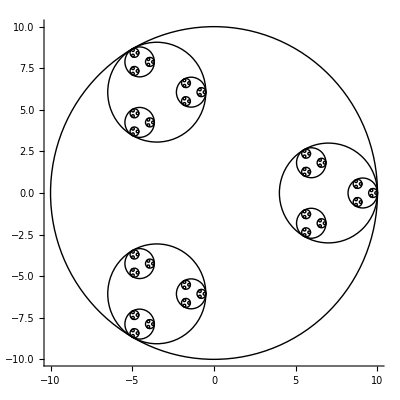

```mathematica
Graphics[Map[createcircles,NestList[newcenters,{{{0,0},10}},4]],Axes->True]
```

```mathematica
NestList[newcenters,{{{0,0},10}},4]
```

{{{{0,0},10}},{{{-3.5,6.06218},3.},{{-3.5,-6.06218},3.},{{7.,0.},3.}},{{{-4.55,7.88083},0.9},{{-4.55,4.24352},0.9},{{-1.4,6.06218},0.9},{{-4.55,-4.24352},0.9},{{-4.55,-7.88083},0.9},{{-1.4,-6.06218},0.9},{{5.95,1.81865},0.9},{{5.95,-1.81865},0.9},{{9.1,0.},0.9}},{{{-4.865,8.42643},0.27},{{-4.865,7.33524},0.27},{{-3.92,7.88083},0.27},{{-4.865,4.78912},0.27},{{-4.865,3.69793},0.27},{{-3.92,4.24352},0.27},{{-1.715,6.60777},0.27},{{-1.715,5.51658},0.27},{{-0.77,6.06218},0.27},{{-4.865,-3.69793},0.27},{{-4.865,-4.78912},0.27},{{-3.92,-4.24352},0.27},{{-4.865,-7.33524},0.27},{{-4.865,-8.42643},0.27},{{-3.92,-7.88083},0.27},{{-1.715,-5.51658},0.27},{{-1.715,-6.60777},0.27},{{-0.77,-6.06218},0.27},{{5.635,2.36425},0.27},{{5.635,1.27306},0.27},{{6.58,1.81865},0.27},{{5.635,-1.27306},0.27},{{5.635,-2.36425},0.27},{{6.58,-1.81865},0.27},{{8.785,0.545596},0.27},{{8.785,-0.545596},0.27},{{9.73,0.},0.27}},{{{-4.9595,8.59011},0.081},{{-4.9595,8.26275},0.081},{{-4.676,8.42643},0.081},{{-4.9595,7.49891},0.081},{{-4.9595,7.17156},0.081},{{-4.676,7.33524},0.081},{{-4.0145,8.04451},0.081},{{-4.0145,7.71715},0.081},{{-3.731,7.88083},0.081},{{-4.9595,4.9528},0.081},{{-4.9595,4.62544},0.081},{{-4.676,4.78912},0.081},{{-4.9595,3.86161},0.081},{{-4.9595,3.53425},0.081},{{-4.676,3.69793},0.081},{{-4.0145,4.4072},0.081},{{-4.0145,4.07985},0.081},{{-3.731,4.24352},0.081},{{-1.8095,6.77145},0.081},{{-1.8095,6.4441},0.081},{{-1.526,6.60777},0.081},{{-1.8095,5.68026},0.081},{{-1.8095,5.3529},0.081},{{-1.526,5.51658},0.081},{{-0.8645,6.22586},0.081},{{-0.8645,5.8985},0.081},{{-0.581,6.06218},0.081},{{-4.9595,-3.53425},0.081},{{-4.9595,-3.86161},0.081},{{-4.676,-3.69793},0.081},{{-4.9595,-4.62544},0.081},{{-4.9595,-4.9528},0.081},{{-4.676,-4.78912},0.081},{{-4.0145,-4.07985},0.081},{{-4.0145,-4.4072},0.081},{{-3.731,-4.24352},0.081},{{-4.9595,-7.17156},0.081},{{-4.9595,-7.49891},0.081},{{-4.676,-7.33524},0.081},{{-4.9595,-8.26275},0.081},{{-4.9595,-8.59011},0.081},{{-4.676,-8.42643},0.081},{{-4.0145,-7.71715},0.081},{{-4.0145,-8.04451},0.081},{{-3.731,-7.88083},0.081},{{-1.8095,-5.3529},0.081},{{-1.8095,-5.68026},0.081},{{-1.526,-5.51658},0.081},{{-1.8095,-6.4441},0.081},{{-1.8095,-6.77145},0.081},{{-1.526,-6.60777},0.081},{{-0.8645,-5.8985},0.081},{{-0.8645,-6.22586},0.081},{{-0.581,-6.06218},0.081},{{5.5405,2.52793},0.081},{{5.5405,2.20057},0.081},{{5.824,2.36425},0.081},{{5.5405,1.43674},0.081},{{5.5405,1.10938},0.081},{{5.824,1.27306},0.081},{{6.4855,1.98233},0.081},{{6.4855,1.65497},0.081},{{6.769,1.81865},0.081},{{5.5405,-1.10938},0.081},{{5.5405,-1.43674},0.081},{{5.824,-1.27306},0.081},{{5.5405,-2.20057},0.081},{{5.5405,-2.52793},0.081},{{5.824,-2.36425},0.081},{{6.4855,-1.65497},0.081},{{6.4855,-1.98233},0.081},{{6.769,-1.81865},0.081},{{8.6905,0.709275},0.081},{{8.6905,0.381917},0.081},{{8.974,0.545596},0.081},{{8.6905,-0.381917},0.081},{{8.6905,-0.709275},0.081},{{8.974,-0.545596},0.081},{{9.6355,0.163679},0.081},{{9.6355,-0.163679},0.081},{{9.919,0.},0.081}}}

```mathematica
newcenter[vecchio_List,vecchioraggio_]:= Table[{{traslax[vecchio[[1]],vecchioraggio,i],traslay[vecchio[[2]],vecchioraggio,i]},vecchioraggio*rapporto},{i,M}];

newcenters[vecchi_List]:= Flatten[Table[newcenter[vecchi[[j,1]],vecchi[[j,2]]],{j,Length[vecchi]}],1];
```

```mathematica
traslax[x0_,r0_,teta0_]:= x0+(r0*(1-rapporto)*Cos[(2*Pi* teta0)/M]);
traslay[y0_,r0_,teta0_]:= y0 + (r0*(1-rapporto)*Sin[(2*Pi *teta0)/M]);
```

```mathematica
createcircles[c_List]:=Table[Circle[{Part[Part[c[[i]],1],1],Part[Part[c[[i]],1],2]},Part[c[[i]],2]],{i,Length[c]}];
```

```mathematica
doit3[proportion_,multiplication_]:=Module[{a={{}},b={}},(rapporto=proportion;M=multiplication;a[[1]]={{{0,0},10}};b=Append[b,createcircles[a[[1]]]];Table[(a=Append[a,newcenters[a[[i]]]];b=Append[b,createcircles[newcenters[a[[i]]]]]),{i,4}])];
```

```mathematica
doit4[proportion_,multiplication_]:= Module[{a,b},(rapporto=proportion;M=multiplication;
a=NestList[newcenters,{{{0,0},10}},4];b=Map[createcircles,a])];
```

```mathematica
doitall[proportion_,multiplication_]:=Graphics[doit3[proportion,multiplication],Axes->True]
```

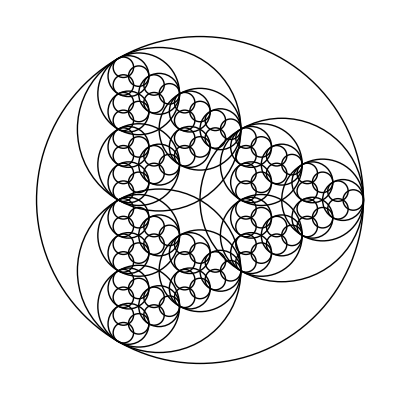

```mathematica
Graphics[doit4[0.5,3]]
```

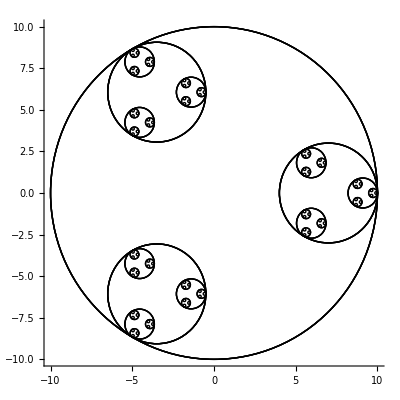

```mathematica
doitall[0.3,3]
```

```mathematica
doit3[0.3,3]
```

{{{Circle[{0,0},10]},{Circle[{-3.5,6.06218},3.],Circle[{-3.5,-6.06218},3.],Circle[{7.,0.},3.]}},{{Circle[{0,0},10]},{Circle[{-3.5,6.06218},3.],Circle[{-3.5,-6.06218},3.],Circle[{7.,0.},3.]},{Circle[{-4.55,7.88083},0.9],Circle[{-4.55,4.24352},0.9],Circle[{-1.4,6.06218},0.9],Circle[{-4.55,-4.24352},0.9],Circle[{-4.55,-7.88083},0.9],Circle[{-1.4,-6.06218},0.9],Circle[{5.95,1.81865},0.9],Circle[{5.95,-1.81865},0.9],Circle[{9.1,0.},0.9]}},{{Circle[{0,0},10]},{Circle[{-3.5,6.06218},3.],Circle[{-3.5,-6.06218},3.],Circle[{7.,0.},3.]},{Circle[{-4.55,7.88083},0.9],Circle[{-4.55,4.24352},0.9],Circle[{-1.4,6.06218},0.9],Circle[{-4.55,-4.24352},0.9],Circle[{-4.55,-7.88083},0.9],Circle[{-1.4,-6.06218},0.9],Circle[{5.95,1.81865},0.9],Circle[{5.95,-1.81865},0.9],Circle[{9.1,0.},0.9]},{Circle[{-4.865,8.42643},0.27],Circle[{-4.865,7.33524},0.27],Circle[{-3.92,7.88083},0.27],Circle[{-4.865,4.78912},0.27],Circle[{-4.865,3.69793},0.27],Circle[{-3.92,4.24352},0.27],Circle[{-1.715,6.60777},0.27],Circle[{-1.715,5.51658},0.27],Circle[{-0.77,6.06218},0.27],Circle[{-4.865,-3.69793},0.27],Circle[{-4.865,-4.78912},0.27],Circle[{-3.92,-4.24352},0.27],Circle[{-4.865,-7.33524},0.27],Circle[{-4.865,-8.42643},0.27],Circle[{-3.92,-7.88083},0.27],Circle[{-1.715,-5.51658},0.27],Circle[{-1.715,-6.60777},0.27],Circle[{-0.77,-6.06218},0.27],Circle[{5.635,2.36425},0.27],Circle[{5.635,1.27306},0.27],Circle[{6.58,1.81865},0.27],Circle[{5.635,-1.27306},0.27],Circle[{5.635,-2.36425},0.27],Circle[{6.58,-1.81865},0.27],Circle[{8.785,0.545596},0.27],Circle[{8.785,-0.545596},0.27],Circle[{9.73,0.},0.27]}},{{Circle[{0,0},10]},{Circle[{-3.5,6.06218},3.],Circle[{-3.5,-6.06218},3.],Circle[{7.,0.},3.]},{Circle[{-4.55,7.88083},0.9],Circle[{-4.55,4.24352},0.9],Circle[{-1.4,6.06218},0.9],Circle[{-4.55,-4.24352},0.9],Circle[{-4.55,-7.88083},0.9],Circle[{-1.4,-6.06218},0.9],Circle[{5.95,1.81865},0.9],Circle[{5.95,-1.81865},0.9],Circle[{9.1,0.},0.9]},{Circle[{-4.865,8.42643},0.27],Circle[{-4.865,7.33524},0.27],Circle[{-3.92,7.88083},0.27],Circle[{-4.865,4.78912},0.27],Circle[{-4.865,3.69793},0.27],Circle[{-3.92,4.24352},0.27],Circle[{-1.715,6.60777},0.27],Circle[{-1.715,5.51658},0.27],Circle[{-0.77,6.06218},0.27],Circle[{-4.865,-3.69793},0.27],Circle[{-4.865,-4.78912},0.27],Circle[{-3.92,-4.24352},0.27],Circle[{-4.865,-7.33524},0.27],Circle[{-4.865,-8.42643},0.27],Circle[{-3.92,-7.88083},0.27],Circle[{-1.715,-5.51658},0.27],Circle[{-1.715,-6.60777},0.27],Circle[{-0.77,-6.06218},0.27],Circle[{5.635,2.36425},0.27],Circle[{5.635,1.27306},0.27],Circle[{6.58,1.81865},0.27],Circle[{5.635,-1.27306},0.27],Circle[{5.635,-2.36425},0.27],Circle[{6.58,-1.81865},0.27],Circle[{8.785,0.545596},0.27],Circle[{8.785,-0.545596},0.27],Circle[{9.73,0.},0.27]},{Circle[{-4.9595,8.59011},0.081],Circle[{-4.9595,8.26275},0.081],Circle[{-4.676,8.42643},0.081],Circle[{-4.9595,7.49891},0.081],Circle[{-4.9595,7.17156},0.081],Circle[{-4.676,7.33524},0.081],Circle[{-4.0145,8.04451},0.081],Circle[{-4.0145,7.71715},0.081],Circle[{-3.731,7.88083},0.081],Circle[{-4.9595,4.9528},0.081],Circle[{-4.9595,4.62544},0.081],Circle[{-4.676,4.78912},0.081],Circle[{-4.9595,3.86161},0.081],Circle[{-4.9595,3.53425},0.081],Circle[{-4.676,3.69793},0.081],Circle[{-4.0145,4.4072},0.081],Circle[{-4.0145,4.07985},0.081],Circle[{-3.731,4.24352},0.081],Circle[{-1.8095,6.77145},0.081],Circle[{-1.8095,6.4441},0.081],Circle[{-1.526,6.60777},0.081],Circle[{-1.8095,5.68026},0.081],Circle[{-1.8095,5.3529},0.081],Circle[{-1.526,5.51658},0.081],Circle[{-0.8645,6.22586},0.081],Circle[{-0.8645,5.8985},0.081],Circle[{-0.581,6.06218},0.081],Circle[{-4.9595,-3.53425},0.081],Circle[{-4.9595,-3.86161},0.081],Circle[{-4.676,-3.69793},0.081],Circle[{-4.9595,-4.62544},0.081],Circle[{-4.9595,-4.9528},0.081],Circle[{-4.676,-4.78912},0.081],Circle[{-4.0145,-4.07985},0.081],Circle[{-4.0145,-4.4072},0.081],Circle[{-3.731,-4.24352},0.081],Circle[{-4.9595,-7.17156},0.081],Circle[{-4.9595,-7.49891},0.081],Circle[{-4.676,-7.33524},0.081],Circle[{-4.9595,-8.26275},0.081],Circle[{-4.9595,-8.59011},0.081],Circle[{-4.676,-8.42643},0.081],Circle[{-4.0145,-7.71715},0.081],Circle[{-4.0145,-8.04451},0.081],Circle[{-3.731,-7.88083},0.081],Circle[{-1.8095,-5.3529},0.081],Circle[{-1.8095,-5.68026},0.081],Circle[{-1.526,-5.51658},0.081],Circle[{-1.8095,-6.4441},0.081],Circle[{-1.8095,-6.77145},0.081],Circle[{-1.526,-6.60777},0.081],Circle[{-0.8645,-5.8985},0.081],Circle[{-0.8645,-6.22586},0.081],Circle[{-0.581,-6.06218},0.081],Circle[{5.5405,2.52793},0.081],Circle[{5.5405,2.20057},0.081],Circle[{5.824,2.36425},0.081],Circle[{5.5405,1.43674},0.081],Circle[{5.5405,1.10938},0.081],Circle[{5.824,1.27306},0.081],Circle[{6.4855,1.98233},0.081],Circle[{6.4855,1.65497},0.081],Circle[{6.769,1.81865},0.081],Circle[{5.5405,-1.10938},0.081],Circle[{5.5405,-1.43674},0.081],Circle[{5.824,-1.27306},0.081],Circle[{5.5405,-2.20057},0.081],Circle[{5.5405,-2.52793},0.081],Circle[{5.824,-2.36425},0.081],Circle[{6.4855,-1.65497},0.081],Circle[{6.4855,-1.98233},0.081],Circle[{6.769,-1.81865},0.081],Circle[{8.6905,0.709275},0.081],Circle[{8.6905,0.381917},0.081],Circle[{8.974,0.545596},0.081],Circle[{8.6905,-0.381917},0.081],Circle[{8.6905,-0.709275},0.081],Circle[{8.974,-0.545596},0.081],Circle[{9.6355,0.163679},0.081],Circle[{9.6355,-0.163679},0.081],Circle[{9.919,0.},0.081]}}}